```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
CoordinateChartData["Spherical","Metric",{r,θ,φ}]
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
ΓMathematica = ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Spherical","Metric",{r,θ,φ}],{r,θ,φ},"Kind"->"Second"]
```

{{{0,0,0},{0,-r,0},{0,0,-r Sin[θ]^2}},{{0,1/r,0},{1/r,0,0},{0,0,-Cos[θ] Sin[θ]}},{{0,0,1/r},{0,0,Cot[θ]},{1/r,Cot[θ],0}}}

```mathematica
(*ΓMathematica[[i, j, k]] = Γ^i_{k j}*)
```

```mathematica
Clear[Γ]
```

```mathematica
Γ[r_]:=
ResourceFunction["ChristoffelSymbol"][g[r], {r, θ}] // FullSimplify
```

```mathematica
(*\Nabla_r v^r*)
Δrvr[r_]:=v'[r]+v[r]Γ[r][[1,1,1]]
(*\Nabla_\theta v^theta*)
Δθvθ[r_]:=v[r]Γ[r][[2,2,1]]
```

```mathematica
Γ[r]
```

{{{(z'[r] z''[r])/(1+z'[r]^2),0},{0,-r/(1+z'[r]^2)}},{{0,1/r},{1/r,0}}}

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
normal[x_]:=Cross[e[1][x],e[2][x]]/Norm[Cross[e[1][x],e[2][x]]]
```

```mathematica
N3dr[x_]:=-{Cos[x[[2]]], Sin[x[[2]]],0} 
N3dR[x_]:={Cos[x[[2]]], Sin[x[[2]]],0} 
N3dγ[x_]:={Cos[x[[2]]], Sin[x[[2]]],0}
```

```mathematica
Ntr[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dr[x].e[j][x],{j,1,2}],{i,1,2}]
NtR[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dR[x].e[j][x],{j,1,2}],{i,1,2}]
Ntγ[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dγ[x].e[j][x],{j,1,2}],{i,1,2}]
```

```mathematica
Ntr[{r,θ}]//FullSimplify
NtR[{r,θ}]//FullSimplify
Ntγ[{r,θ}]//FullSimplify
```

{-1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

```mathematica
nr[x_]:=Ntr[x]/Sqrt[Sum[Ntr[x][[i]] Ntr[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nR[x_]:=NtR[x]/Sqrt[Sum[NtR[x][[i]] NtR[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nγ[x_]:=Ntγ[x]/Sqrt[Sum[Ntγ[x][[i]] Ntγ[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
```

```mathematica
nγ[{r,θ}]
```

{√(1/(1+z'[r]^2)),0}

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in \Nalba_i \Nabla^i H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
(* NablaNablaH = \Nalba_i \Nabla^i H*)
```

```mathematica
NablaNablaH[r_]:=1/sqrtdetg[r] ϕ'[r]
```

```mathematica
(*fVISC[r] = f^{VISC r}_notes*)
```

```mathematica
fVISCt[r_]:=1/(1+z'[r]^2)2 η (v''[r]+(v'[r] z'[r] z''[r])/(1+z'[r]^2)-(2 v[r] z'[r]^2 z''[r]^2)/((1+z'[r]^2)^2)+(v[r] z''[r]^2)/(1+z'[r]^2)+(-v[r]/r+v'[r]+(v[r] z'[r] z''[r])/(1+z'[r]^2))/r+(v[r] z'[r] Derivative[3][z][r])/(1+z'[r]^2))
```

```mathematica
fσt[r_]:=ig[r][[1,1]]σ'[r]
```

```mathematica
fvt[r_]:=ρ v[r]Δrvr[r]
```

```mathematica
(*d[r][[i,j]] = d_{ij}_notes*)
```

```mathematica
d[r_]:={{g[r][[1,1]]Δrvr[r],0},{0,g[r][[2,2]]Δθvθ[r]}}
```

```mathematica
(*Π[r_][[i,j]]= \Pi^{ij}_notes*)
```

```mathematica
Π[r_]:=Table[Table[-σ[r]ig[r][[i,j]]-2 η ig[r][[i,i]]ig[r][[j,j]]d[r][[i,j]],{j,1,2}],{i,1,2}]
```

```mathematica
(*force per unit length due to viscosity and surface tension exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlησt[r_]:=Table[Sum[Π[r][[i,j]] g[r][[j, k]]*nγ[{r,θ}][[k]],{j,1,2},{k,1,2}],{i,1,2}]
```

```mathematica
(*tangent force per unit length due to κ exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlκt[r_]:=Table[-2 κ H[r]^2 nγ[{r,θ}][[i]],{i,1,2}]
```

```mathematica
(*normal force per unit length due to κ exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlκn[r_]:=2 κ H'[r] nγ[{r,θ}][[1]]
```

```mathematica
(*tangent force per unit length, in the 3d space, due to σ and η exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlησ3d[r_,θ_]:=Sum[dFdlησt[r][[i]]e[i][{r,θ}],{i,1,2}]
```

```mathematica
(*tangent force per unit length, in the 3d space, due to κ exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlκ3d[r_,θ_]:=Sum[dFdlκt[r][[i]]e[i][{r,θ}],{i,1,2}] +dFdlκn[r] normal[{r,θ}]
```

```mathematica
(*relation between v and z' given by the continuity equation*)
```

```mathematica
repv={v[r]->C1/(r √(1+(z'[r])^2)),v'[r]->-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2)),v''[r]->1/(r^3 (1+z'[r]^2)^(5/2))C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r Derivative[3][z][r])+r z'[r]^3 (2 z''[r]-r Derivative[3][z][r]))};
```

```mathematica
Clear[dFdlησ3d]
dFdlησ3d[r_,θ_]:={(Cos[θ] (-σ[r]/(1+z'[r]^2)-(2 ((z'[r] z''[r])/(r (1+z'[r]^2)^(3/2))-(1+z'[r]^2+r z'[r] z''[r])/(r^2 (1+z'[r]^2)^(3/2))))/(1+z'[r]^2)))/(√(1/(1+z'[r]^2))),(Sin[θ] (-σ[r]/(1+z'[r]^2)-(2 ((z'[r] z''[r])/(r (1+z'[r]^2)^(3/2))-(1+z'[r]^2+r z'[r] z''[r])/(r^2 (1+z'[r]^2)^(3/2))))/(1+z'[r]^2)))/(√(1/(1+z'[r]^2))),(z'[r] (-σ[r]/(1+z'[r]^2)-(2 ((z'[r] z''[r])/(r (1+z'[r]^2)^(3/2))-(1+z'[r]^2+r z'[r] z''[r])/(r^2 (1+z'[r]^2)^(3/2))))/(1+z'[r]^2)))/(√(1/(1+z'[r]^2)))}
```

```mathematica
Clear[dFdlκ3d]
dFdlκ3d[r_,θ_]:={-(κ Cos[θ] (1/(1+z'[r]^2))^(7/2) (z'[r]+z'[r]^3+r z''[r])^2)/(2 r^2)-1/(√(1+z'[r]^2))2 κ Cos[θ] z'[r] √(1/(1+z'[r]^2)) ((r (z'[r]+z'[r]^3+r z''[r]))/((r^2 (1+z'[r]^2))^(3/2))-(3 r^2 (z'[r]+z'[r]^3+r z''[r]) (2 r (1+z'[r]^2)+2 r^2 z'[r] z''[r]))/(4 (r^2 (1+z'[r]^2))^(5/2))+(r^2 (2 z''[r]+3 z'[r]^2 z''[r]+r Derivative[3][z][r]))/(2 (r^2 (1+z'[r]^2))^(3/2))),-(κ Sin[θ] (1/(1+z'[r]^2))^(7/2) (z'[r]+z'[r]^3+r z''[r])^2)/(2 r^2)-1/(√(1+z'[r]^2))2 κ Sin[θ] z'[r] √(1/(1+z'[r]^2)) ((r (z'[r]+z'[r]^3+r z''[r]))/((r^2 (1+z'[r]^2))^(3/2))-(3 r^2 (z'[r]+z'[r]^3+r z''[r]) (2 r (1+z'[r]^2)+2 r^2 z'[r] z''[r]))/(4 (r^2 (1+z'[r]^2))^(5/2))+(r^2 (2 z''[r]+3 z'[r]^2 z''[r]+r Derivative[3][z][r]))/(2 (r^2 (1+z'[r]^2))^(3/2))),-(κ z'[r] (1/(1+z'[r]^2))^(7/2) (z'[r]+z'[r]^3+r z''[r])^2)/(2 r^2)+1/(√(1+z'[r]^2))2 κ √(1/(1+z'[r]^2)) ((r (z'[r]+z'[r]^3+r z''[r]))/((r^2 (1+z'[r]^2))^(3/2))-(3 r^2 (z'[r]+z'[r]^3+r z''[r]) (2 r (1+z'[r]^2)+2 r^2 z'[r] z''[r]))/(4 (r^2 (1+z'[r]^2))^(5/2))+(r^2 (2 z''[r]+3 z'[r]^2 z''[r]+r Derivative[3][z][r]))/(2 (r^2 (1+z'[r]^2))^(3/2)))}
```

```mathematica
dFdltot3d[r_,θ_]:=dFdlησ3d[r,θ]+dFdlκ3d[r,θ]
```

```mathematica
FullSimplify[D[D[C1/(r √(1+(z'[r])^2)),r],r],Assumptions->ass]
```

1/(r^3 (1+z'[r]^2)^(5/2))C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r z^(3)[r])+r z'[r]^3 (2 z''[r]-r z^(3)[r]))

```mathematica
eqs=FullSimplify[{   
ρ v[r]Δrvr[r]==ig[r][[1,1]]σ'[r]+2 η ig[r][[1,1]]( (D[Δrvr[r],r])+(Δrvr[r]-Δθvθ[r])Γ[r][[2,2,1]]),
ρ (v[r]^2) b[r][[1,1]]== κ(-2 NablaNablaH[r] -4H[r](H[r]^2-K[r]))+2 σ[r] H[r] +2 η (ig[r][[1,1]]Δrvr[r]b[r][[1,1]] + ig[r][[2,2]]Δθvθ[r]b[r][[2,2]])
},Assumptions->ass]
```

{ρ v[r] (v'[r]+(v[r] z'[r] z''[r])/(1+z'[r]^2))==1/(r^2 (1+z'[r]^2)^3)(r (1+z'[r]^2) ((1+z'[r]^2) (r σ'[r]+2 η (v'[r]+r v''[r]))+2 r η v'[r] z'[r] z''[r])+2 η v[r] (-1-z'[r]^4+r^2 z''[r]^2-z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (z''[r]+r z^(3)[r])+r z'[r]^3 (z''[r]+r z^(3)[r]))),1/(2 (1+z'[r]^2)^(9/2))((κ z'[r] (1+z'[r]^2)^3)/r^3+(κ z'[r] (1+z'[r]^2)^4)/r^3-(4 η v[r] z'[r] (1+z'[r]^2)^4)/r^2-(2 σ[r] z'[r] (1+z'[r]^2)^4)/r-(3 κ (1+z'[r]^2)^2 z''[r])/r^2+(κ (1+z'[r]^2)^3 z''[r])/r^2-2 σ[r] (1+z'[r]^2)^3 z''[r]-4 η v'[r] (1+z'[r]^2)^3 z''[r]+2 ρ v[r]^2 (1+z'[r]^2)^4 z''[r]-(15 κ z'[r] (1+z'[r]^2) z''[r]^2)/r-4 η v[r] z'[r] (1+z'[r]^2)^2 z''[r]^2-35 κ z''[r]^3+30 κ (1+z'[r]^2) z''[r]^3+(4 κ (1+z'[r]^2)^2 z^(3)[r])/r-20 κ z'[r] (1+z'[r]^2) z''[r] z^(3)[r]+2 κ (1+z'[r]^2)^2 z^(4)[r])==0}

```mathematica
eqs=FullSimplify[eqs/.repv,Assumptions->ass]
```

$Aborted

```mathematica
Clear[κ,η,ρ]
```

```mathematica
Clear[C1]
```

```mathematica
(*
To produce figure-6:
Rmin=1/100;
Rmax=1/2;
κ=3*^-2;
η=1*^-2;
ρ=1*^-12;
C1=1;
zpRmin=1/10;
zRmin=-1/10;
zppRmin=0;
σRmax=1;
bcs={
σ[Rmax]==σRmax,
z[Rmin]==zRmin,z'[Rmin]==zpRmin,z[Rmax]==0,z'[Rmax]==0
};
sol=NDSolve[...]
*)
```

```mathematica
Rmin=1;
Rmax=2;
```

```mathematica
κ=1;
η=1;
ρ=1;
C1=1;
```

```mathematica
Solve[eqs[[2]]/.{r->Rmin}/.{z'[Rmin]->1/10,z''[Rmin]->0,z'''[Rmin]->0,z''''[Rmin]->0},σ[1]]
```

{{σ[1]→1/202 (201-40 √101)}}

```mathematica
bcs={
σ[Rmin]==1/202 (201-40 √101),
z'[Rmin]==1/10,z''[Rmin]==0,z'''[Rmin]==0,z''''[Rmin]==0
};
```

```mathematica
sol=NDSolve[Flatten[{eqs,bcs}],{σ,z},{r,Rmin,Rmax},WorkingPrecision->30][[1]]
```

{σ→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
(*Boundary conditions to feed into the finite-element code*)
```

```mathematica
(*σ[Rmin] = sigma_r_const in variatinal_problem_bc_ring.py*)
```

```mathematica
N[1/202 (201-40 √101),20]
```

-0.99502487546948322183

```mathematica
npts=3;
rGrid=Subdivide[Rmin,Rmax,npts-1];
dr=(rMax-rMin)/(npts-1);
zIF[r_]:=Evaluate[z[r]/. First@sol];
vIF[r_]:=Evaluate[(v[r]/. repv)/. sol];
vPrimeIF[r_] :=Evaluate[D[vIF[r],r]];
z1IF=zIF';
z2IF=z1IF';
(*z3IF = z2IF';
z4IF = z3IF';*)
HIF[r_] := Evaluate[H[r] /. sol];
sigmaIF[r_] := Evaluate[σ[r]/. sol];
HPrimeIF[r_] :=Evaluate[(H'[r])/. sol];
lapHIF[r_]:=Evaluate[NablaNablaH[r]/. sol];
(*ffVISCtNum[r_]:=Evaluate[fVISCt[r]/.repv/.sol];
fsigmatNum[r_]:=Evaluate[fsigmat[r]/. sol];
fvtNum[r_]:=Evaluate[fvt[r]/. sol];
dFdletasigmatNum[r_]:=Evaluate[dFdletasigmat[r]/. sol];
dFdlkappatNum[r_]:=Evaluate[dFdlkappat[r]/. sol];
dFdlkappanNum[r_]:=Evaluate[dFdlkappan[r]/. sol];
brrIF[r_]:=Evaluate[z2IF[r]/Sqrt[1+(z1IF[r])^2]];*)
(*Plot[brrIF[r],{r,rMin,rMax}]*)
zStar=zIF/@rGrid;
zPrime=z1IF/@rGrid;
zDouble=z2IF/@rGrid;
(*zTriple = z3IF /@rGrid;
zQuad = z4IF /@rGrid;*)
vStar=vIF/@rGrid;
vPrimeStar = vPrimeIF /@ rGrid;
brrStar = brrIF /@ rGrid;
sigmaStar = sigmaIF /@ rGrid;
HStar=HIF/@rGrid;
HPrimeStar=HPrimeIF/@rGrid;
NablaNablaHStar=lapHIF/@rGrid;
(*ffVISCtStar=ffVISCtNum/@rGrid;
fsigmatStar=fsigmatNum/@rGrid;
fvtStar=fvtNum/@rGrid;
dFdletasigmatStar=dF_dletasigmatNum/@rGrid;
dFdlkappatStar=dF_dlkappatNum/@rGrid;
dFdlkappanStar=dF_dlkappanNum/@rGrid;*)
Plot[vPrimeIF[r], {r, Rmin, Rmax}]
ListPlot[Transpose[{rGrid,HStar}],PlotStyle->Blue,Joined->True,AxesLabel->{"r","z(r)"},PlotMarkers->Automatic]
data=Transpose[{rGrid,zStar,zPrime(*,zDouble,zTriple*),zQuad,vStar,vPrimeStar,sigmaStar,HStar,HPrimeStar,NablaNablaHStar(*,ffVISCtStar,fsigmatStar,fvtStar,dFdletasigmatStar,dFdlkappatStar,dFdlkappanStar*)}];
header={"r","z(r)","z'(r)",(*"z''(r)","z'''(r)"*),"z''''(r)","v(r)","v'(r)","sigma(r)","H(r)","H'(r)","∇∇H(r)"(*,"ffVISCt(r)","fsigmat(r)","fvt(r)","dF/dletasigmat(r)","dF/dlkappat(r)","dF/dlkappan(r)"*)};
dataWithHeader=Prepend[data,header];

Export["C:\\Universität\\Projekte\\Praktikum_SS_25\\My_own_experiments\\Stability_Radialsymmetry\\solution_1D.csv",dataWithHeader]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

D::ivar: Rmax/2+Rmin/2 is not a valid variable.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Plot::plln: Limiting value Rmin in {r,Rmin,Rmax} is not a machine-sized real number.

Plot[vPrimeIF[r],{r,Rmin,Rmax}]

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

Transpose::nmtx: The first two levels of {{Rmin,Rmax/2+Rmin/2,Rmax},«8»,{((2 Rmin (Times[«3»]+«1»+Times[«4»]))/(√Plus[«2»])-(«1»)/(2«1»«1»)+((«4»)^2 («1»))/(√Plus[«2»]))/(√(Rmin^2+Power[«2»] Power[«2»]))/.sol,(«1»)/(√(«1»+«1»))/.sol,((«1»)/(√(«1»))-(«1»)/(«1»)+(«1»)/(√(«1»)))/(«1»)/.sol}} cannot be transposed.

Transpose::tperm: Permutation {{Rmin,Rmax/2+Rmin/2,Rmax},«8»,{((2 Rmin (Times[«3»]+«1»+Times[«4»]))/(√Plus[«2»])-(«1»)/(2«1»«1»)+((«4»)^2 («1»))/(√Plus[«2»]))/(√(Rmin^2+Power[«2»] Power[«2»]))/.sol,(«1»)/(√(«1»+«1»))/.sol,((«1»)/(√(«1»))-(«1»)/(«1»)+(«1»)/(√(«1»)))/(«1»)/.sol}} is longer than the dimensions {11} of the expression.

C:\Universität\Projekte\Praktikum_SS_25\My_own_experiments\Stability_Radialsymmetry\solution_1D.csv

```mathematica
Directory[]
```

C:\Users\ruben

```mathematica
(*z[Rmin] = z_r_const in variational_problem_bc_ring.py*)
```

```mathematica
z[r]/.{r->Rmin}/.sol
```

1.

```mathematica
(*z[Rmax]= z_R_const in variational_problem_bc_ring.py*)
```

```mathematica
z[r]/.{r->Rmax}/.sol
```

1.0990007696349066183303716066

```mathematica
(*n^i omega_i_{at r = Rmin} = omega_r_const in variational_problem_bc_ring.py*)
```

```mathematica
(Sum[{z'[r],0}[[i]]* nr[{r,θ}][[i]],{i,1,2}])/.repv/.sol/.{r->Rmin}
```

-0.099503719020998913567

```mathematica
(*n^i omega_i at r = Rmax = omega_R_const in variational_problem_bc_ring.py*)
```

```mathematica
(Sum[{z'[r],0}[[i]]* nR[{r,θ}][[i]],{i,1,2}])/.repv/.sol/.{r->Rmax}
```

0.095353866240961546555843199533

```mathematica
(*v[Rmin] = v_r_const in variational_problem_bc_ring.py*)
```

```mathematica
v[r]/.repv/.{r->Rmin}/.sol
```

0.9950371902099891356653

```mathematica
(*v^i n_i_{r = Rmax} = v_R_const in variational_problem_bc_ring.py *)
```

```mathematica
(Sum[{v[r],0}[[i]]* nR[{r,θ}][[j]] g[r][[i,j]],{i,1,2},{j,1,2}])/.repv/.sol/.{r->Rmax}
```

0.5

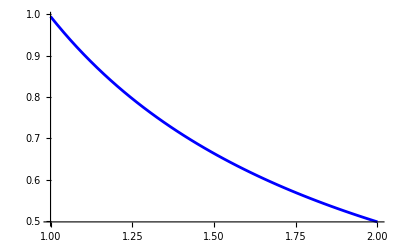

```mathematica
plotvexact=Plot[v[r]/.repv/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

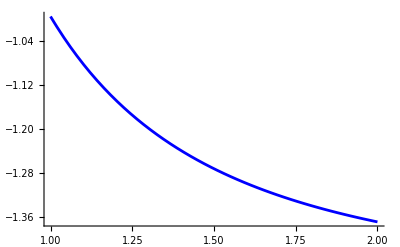

```mathematica
plotσexact=Plot[Evaluate[σ[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

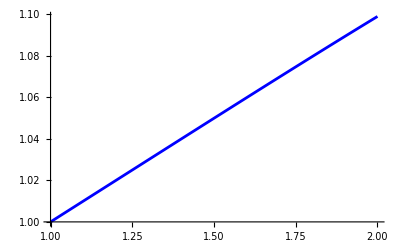

```mathematica
plotzexact=Plot[Evaluate[z[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

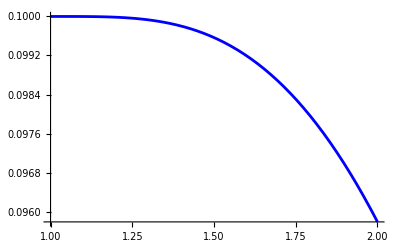

```mathematica
plotωexact=Plot[z'[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

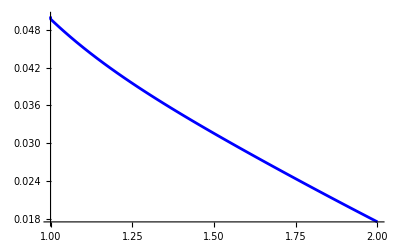

```mathematica
plotμexact=Plot[H[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

```mathematica
delta=1/100;
```

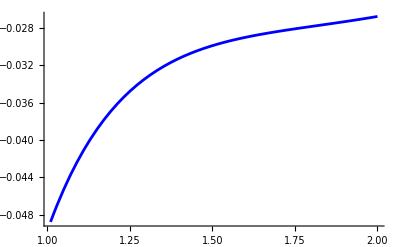

```mathematica
plotνexact=Plot[Evaluate[H'[r]/. sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

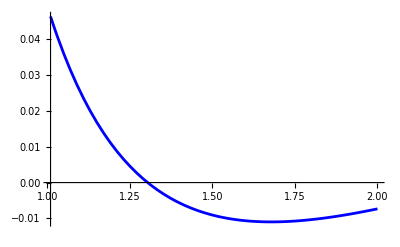

```mathematica
plotτexact=Plot[Evaluate[NablaNablaH[r]/. sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

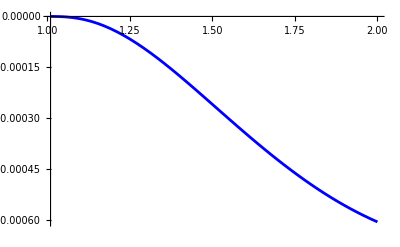

```mathematica
plotfVISCtexact=Plot[Evaluate[fVISCt[r]/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

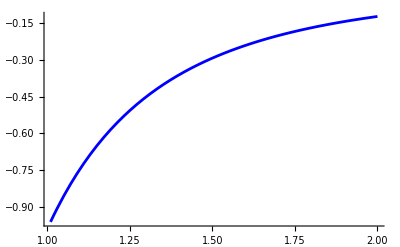

```mathematica
plotfσtexact=Plot[Evaluate[fσt[r]/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

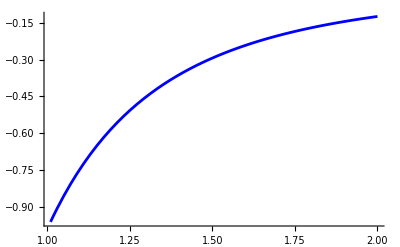

```mathematica
plotfvtexact=Plot[Evaluate[fvt[r]/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

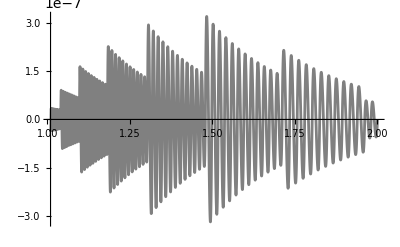

```mathematica
plotftottexact=Plot[Evaluate[(fvt[r]-fσt[r]-fVISCt[r])/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Gray]
```

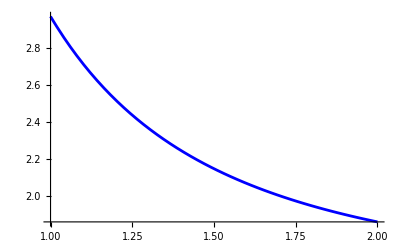

```mathematica
plotdFdlησtexact=  Plot[Evaluate[dFdlησt[r][[1]]/.repv/.sol],{r,Rmin,Rmax},PlotStyle->Blue]
```

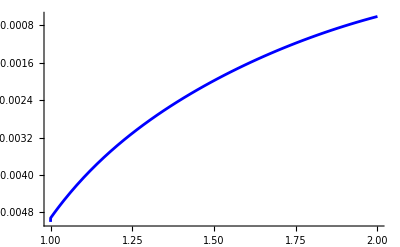

```mathematica
plotdFdlκtexact=  Plot[Evaluate[dFdlκt[r][[1]]/.repv/.sol],{r,Rmin,Rmax},PlotStyle->Blue]
```

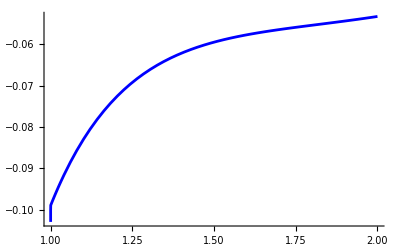

```mathematica
plotdFdlκnexact=  Plot[Evaluate[dFdlκn[r]/.repv/.sol],{r,Rmin,Rmax},PlotStyle->Blue]
```

```mathematica
plotdFdlησ3dexact={ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlησ3d[r,θ][[1]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlησ3d[r,θ][[2]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlησ3d[r,θ][[3]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]}
```

$Aborted

```mathematica
plotdFdlκ3dexact={ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlκ3d[r,θ][[1]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlκ3d[r,θ][[2]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlκ3d[r,θ][[3]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
plotdFdltot3dexact={ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdltot3d[r,θ][[1]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdltot3d[r,θ][[2]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdltot3d[r,θ][[3]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*total force exerted on ds_r*)
```

```mathematica
Table[NIntegrate[N[dFdltot3d[Rmin,θ][[i]]/.sol] Rmin ,{θ,0,2π}],{i,1,3}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.94515}. NIntegrate obtained -1.70697×10^-15 and 6.99685×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.41777}. NIntegrate obtained -1.01308×10^-15 and 1.59469×10^-15 for the integral and error estimates.

{-1.70697×10^-15,-1.01308×10^-15,1.24418}

```mathematica
(*Compare with the solution from FE*)
```

```mathematica
(*check of v*)
```

```mathematica
tabv=Import["C:\\Universität\\Projekte\\Praktikum_SS_25\\New_Project\\steady-state-flow\\solution\\v.csv\"];
tabv=Table[{Norm[{tabv[[i,4]],tabv[[i,5]]}],{tabv[[i, 4]], tabv[[i, 5]]}/Norm[{tabv[[i, 4]], tabv[[i, 5]]}].{tabv[[i,1]],tabv[[i,2]]}},{i,2,Length[tabv]}]
plotvfe=ListPlot[tabv,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

Import::nffil: File /workspace/steady-state-flow/solution/v.csv not found during Import.

{}

-Graphics-

```mathematica
Show[plotvfe,plotvexact]
```

Show::gcomb: Could not combine the graphics objects in Show[plotvfe,].

Show[plotvfe,-Graphics-]

```mathematica
(*check of sigma*)
```

```mathematica
tabσ=Import["~/Documents/finite_elements/steady-state-flow/solution/sigma.csv"];
tabσ=Table[{Norm[{tabσ[[i,2]],tabσ[[i,3]]}],tabσ[[i,1]]},{i,2,Length[tabσ]}]
plotσfe=ListPlot[tabσ,PlotRange->Full,PlotStyle->{PointSize->.005,Red,Opacity[1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/sigma.csv not found during Import.

{}

-Graphics-

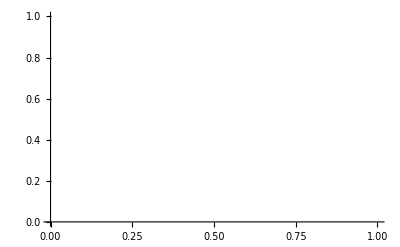

```mathematica
Show[plotσfe,plotσexact]
```

```mathematica
(*check of z*)
```

```mathematica
tabz=Import["~/Documents/finite_elements/steady-state-flow/solution/z.csv"];
tabz=Table[{Norm[{tabz[[i,2]],tabz[[i,3]]}],tabz[[i,1]]},{i,2,Length[tabz]}]
plotzfe=ListPlot[tabz,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/z.csv not found during Import.

{}

-Graphics-

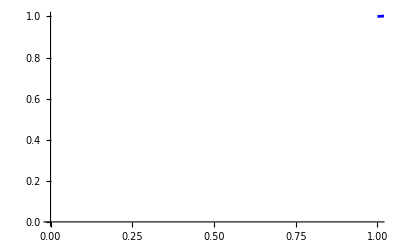

```mathematica
Show[plotzfe,plotzexact]
```

```mathematica
(*check of ω*)
```

```mathematica
tabω=Import["~/Documents/finite_elements/steady-state-flow/solution/omega.csv"];
tabω=Table[{Norm[{tabω[[i,4]],tabω[[i,5]]}],({tabω[[i,4]],tabω[[i,5]]}/Norm[{tabω[[i,4]],tabω[[i,5]]}]).{tabω[[i,1]],tabω[[i,2]]}},{i,2,Length[tabω]}]
plotωfe=ListPlot[tabω,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/omega.csv not found during Import.

{}

-Graphics-

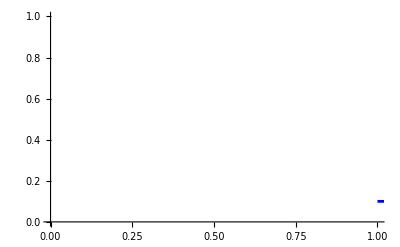

```mathematica
Show[plotωfe,plotωexact]
```

```mathematica
(*check of μ*)
```

```mathematica
tabμ=Import["~/Documents/finite_elements/steady-state-flow/solution/mu.csv"];
tabμ=Table[{Norm[{tabμ[[i,2]],tabμ[[i,3]]}],tabμ[[i,1]]},{i,2,Length[tabμ]}]
plotμfe=ListPlot[tabμ,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/mu.csv not found during Import.

{}

-Graphics-

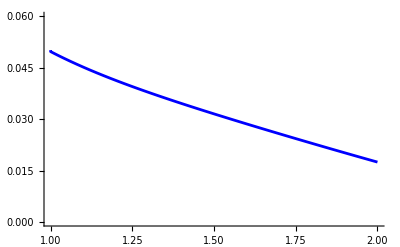

```mathematica
Show[plotμfe,plotμexact,PlotRange->{0,0.06}]
```

```mathematica
(*check nu*)
```

```mathematica
ν=Import["~/Documents/finite_elements/steady-state-flow/solution/nu.csv"];
ν=Table[{Sqrt[ν[[i,4]]^2+ν[[i,5]]^2],ν[[i,4]]/Sqrt[ν[[i,4]]^2+ν[[i,5]]^2] ν[[i,1]]+ν[[i,5]]/Sqrt[ν[[i,4]]^2+ν[[i,5]]^2] ν[[i,2]]},{i,2,Length[ν]}]
plotνnum=ListPlot[ν,PlotStyle->{Red,Opacity->1}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/nu.csv not found during Import.

{}

-Graphics-

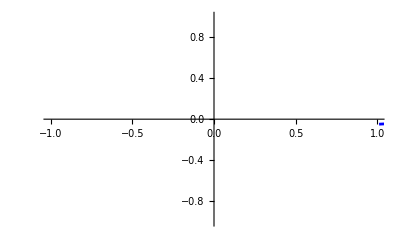

```mathematica
Show[plotνnum,plotνexact]
```

```mathematica
(*check τ*)
```

```mathematica
τnum=Import["~/Documents/finite_elements/steady-state-flow/solution/tau.csv"];
τnum=Table[{Sqrt[τnum[[i,2]]^2+τnum[[i,3]]^2],τnum[[i,1]]},{i,2,Length[τnum]}]
plotτnum=ListPlot[τnum,PlotStyle->{Red,Opacity->0.1}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/tau.csv not found during Import.

{}

-Graphics-

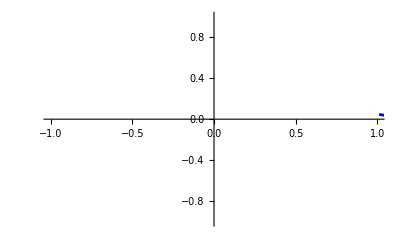

```mathematica
Show[plotτnum,plotτexact]
```

```mathematica
(*check of forces*)
```

```mathematica
(*normal forces*)
```

```mathematica
tabfeln=Import["~/Documents/finite_elements/steady-state-flow/solution/fel_n.csv"];
tabfeln=Table[{Norm[{tabfeln[[i,2]],tabfeln[[i,3]]}],tabfeln[[i,1]]},{i,2,Length[tabfeln]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/fel_n.csv not found during Import.

{}

```mathematica
tabflaplacen=Import["~/Documents/finite_elements/steady-state-flow/solution/flaplace.csv"];
tabflaplacen=Table[{Norm[{tabflaplacen[[i,2]],tabflaplacen[[i,3]]}],tabflaplacen[[i,1]]},{i,2,Length[tabflaplacen]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/flaplace.csv not found during Import.

{}

```mathematica
tabfviscn=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_n.csv"];
tabfviscn=Table[{Norm[{tabfviscn[[i,2]],tabfviscn[[i,3]]}],tabfviscn[[i,1]]},{i,2,Length[tabfviscn]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/fvisc_n.csv not found during Import.

{}

```mathematica
tabftotn=Table[{tabfviscn[[i,1]],tabfeln[[i,2]]+tabflaplacen[[i,2]]+tabfviscn[[i,2]]},{i,2,Length[tabfviscn]}]
```

{}

```mathematica
ListPlot[tabftotn,PlotStyle->Black]
```

-Graphics-

```mathematica
plotfeln=ListPlot[tabfeln,PlotRange->Full,PlotStyle->{PointSize->.01,Green,Opacity[0.1]}]
```

-Graphics-

```mathematica
plotflaplacen=ListPlot[tabflaplacen,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

-Graphics-

```mathematica
plotfviscn=ListPlot[tabfviscn,PlotRange->Full,PlotStyle->{PointSize->.01,Blue,Opacity[0.1]}]
```

-Graphics-

```mathematica
Show[plotfeln,plotflaplacen,plotfviscn,PlotRange->{-0.2,0.2}]
```

-Graphics-

```mathematica
(*tangential forces*)
```

```mathematica
tabfVISCt=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_t.csv"];
tabfVISCt=Table[{Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}],({tabfVISCt[[i,4]],tabfVISCt[[i,5]]}/Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}]).{tabfVISCt[[i,1]],tabfVISCt[[i,2]]}},{i,2,Length[tabfVISCt]}]
plotfVISCtfe=ListPlot[tabfVISCt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/fvisc_t.csv not found during Import.

{}

-Graphics-

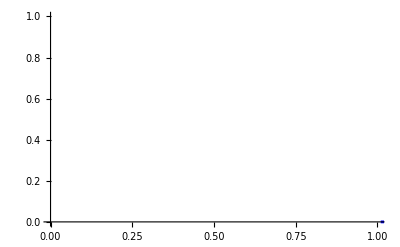

```mathematica
Show[plotfVISCtfe,plotfVISCtexact]
```

```mathematica
tabfσt=Import["~/Documents/finite_elements/steady-state-flow/solution/fsigma_t.csv"];
tabfσt=Table[{Norm[{tabfσt[[i,4]],tabfσt[[i,5]]}],({tabfσt[[i,4]],tabfσt[[i,5]]}/Norm[{tabfσt[[i,4]],tabfσt[[i,5]]}]).{tabfσt[[i,1]],tabfσt[[i,2]]}},{i,2,Length[tabfσt]}]
plotfσtfe=ListPlot[tabfσt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/fsigma_t.csv not found during Import.

{}

-Graphics-

```mathematica
Show[plotfσtfe,plotfσtexact]
```

-Graphics-

```mathematica
tabfvt=Import["~/Documents/finite_elements/steady-state-flow/solution/fv_t.csv"];
tabfvt=Table[{Norm[{tabfvt[[i,4]],tabfvt[[i,5]]}],({tabfvt[[i,4]],tabfvt[[i,5]]}/Norm[{tabfvt[[i,4]],tabfvt[[i,5]]}]).{tabfvt[[i,1]],tabfvt[[i,2]]}},{i,2,Length[tabfvt]}]
plotfvtfe=ListPlot[tabfvt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/fv_t.csv not found during Import.

{}

-Graphics-

```mathematica
Show[plotfvtfe,plotfvtexact]
```

-Graphics-

```mathematica
(*check that the sum fVISCt + fσt- fvt = 0*)
```

```mathematica
tabfVISCt=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_t.csv"];
tabfσt=Import["~/Documents/finite_elements/steady-state-flow/solution/fsigma_t.csv"];
tabfvt=Import["~/Documents/finite_elements/steady-state-flow/solution/fv_t.csv"];
tabftott=Table[{Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}],({tabfVISCt[[i,4]],tabfvt[[i,5]]}/Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}]).{tabfVISCt[[i,1]]+tabfσt[[i,1]]-tabfvt[[i,1]],tabfVISCt[[i,2]]+tabfσt[[i,2]]-tabfvt[[i,2]]}},{i,2,Length[tabfVISCt]}]
plotftottfe=ListPlot[tabftott,PlotRange->{-0.2,0.2},PlotStyle->{PointSize->.01,Blue,Opacity[1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/fvisc_t.csv not found during Import.

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/fsigma_t.csv not found during Import.

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/fv_t.csv not found during Import.

{}

-Graphics-

```mathematica
(*force due to viscosity and surface tension exerted on a line element, dFdlησt*)
```

```mathematica
tabdFdlησt=Import["~/Documents/finite_elements/steady-state-flow/solution/dFdl_eta_sigma_t.csv"];
tabdFdlησt=Table[{Norm[{tabdFdlησt[[i,4]],tabdFdlησt[[i,5]]}],({tabdFdlησt[[i,4]],tabdFdlησt[[i,5]]}/Norm[{tabdFdlησt[[i,4]],tabdFdlησt[[i,5]]}]).{tabdFdlησt[[i,1]],tabdFdlησt[[i,2]]}},{i,2,Length[tabdFdlησt]}]
plotdFdlησtfe=ListPlot[tabdFdlησt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/dFdl_eta_sigma_t.csv not found during Import.

{}

-Graphics-

```mathematica
Show[plotdFdlησtfe,plotdFdlησtexact]
```

-Graphics-

```mathematica
(*tangent force due to bending rigidity  exerted on a line element, dFdlκt*)
```

```mathematica
tabdFdlκt=Import["~/Documents/finite_elements/steady-state-flow/solution/dFdl_kappa_t.csv"];
tabdFdlκt=Table[{Norm[{tabdFdlκt[[i,4]],tabdFdlκt[[i,5]]}],({tabdFdlκt[[i,4]],tabdFdlκt[[i,5]]}/Norm[{tabdFdlκt[[i,4]],tabdFdlκt[[i,5]]}]).{tabdFdlκt[[i,1]],tabdFdlκt[[i,2]]}},{i,2,Length[tabdFdlκt]}]
plotdFdlκt=ListPlot[tabdFdlκt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/dFdl_kappa_t.csv not found during Import.

{}

-Graphics-

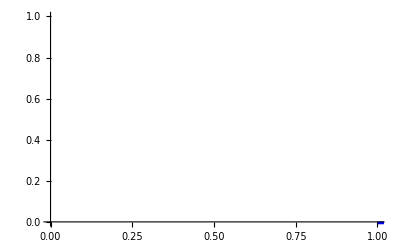

```mathematica
Show[plotdFdlκt,plotdFdlκtexact]
```

```mathematica
(*normal force due to bending rigidity  exerted on a line element, dFdlκn*)
```

```mathematica
tabdFdlκn=Import["~/Documents/finite_elements/steady-state-flow/solution/dFdl_kappa_n.csv"];
tabdFdlκn=Table[{Norm[{tabdFdlκn[[i,2]],tabdFdlκn[[i,3]]}],tabdFdlκn[[i,1]]},{i,2,Length[tabdFdlκn]}]
plotdFdlκn=ListPlot[tabdFdlκn,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[1]}]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/dFdl_kappa_n.csv not found during Import.

{}

-Graphics-

```mathematica
Show[plotdFdlκn,plotdFdlκnexact]
```

-Graphics-

```mathematica
(*test forces per unit length in 3d space*)
```

```mathematica
(*check tabdFdlησ3d*)
tabdFdlησ3d=Import["~/Documents/finite_elements/steady-state-flow/solution/nodal_values/dFdl_eta_sigma_3d.csv"];
tabdFdlησ3d={Table[{tabdFdlησ3d[[i,4]],tabdFdlησ3d[[i,5]],tabdFdlησ3d[[i,1]]},{i,2,Length[tabdFdlησ3d]}],
Table[{tabdFdlησ3d[[i,4]],tabdFdlησ3d[[i,5]],tabdFdlησ3d[[i,2]]},{i,2,Length[tabdFdlησ3d]}],
Table[{tabdFdlησ3d[[i,4]],tabdFdlησ3d[[i,5]],tabdFdlησ3d[[i,3]]},{i,2,Length[tabdFdlησ3d]}]};
plottabdFdlησ3dfe={
ListPointPlot3D[tabdFdlησ3d[[1]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlησ3d[[2]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlησ3d[[3]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[.5]},AxesLabel->{"x","y","z"}]}
Show[plotdFdlησ3dexact[[1]],plottabdFdlησ3dfe[[1]]]
Show[plotdFdlησ3dexact[[2]],plottabdFdlησ3dfe[[2]]]
Show[plotdFdlησ3dexact[[3]],plottabdFdlησ3dfe[[3]]]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/nodal_values/dFdl_eta_sigma_3d.csv not found during Import.

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*check tabdFdlκ3d*)
tabdFdlκ3d=Import["~/Documents/finite_elements/steady-state-flow/solution/nodal_values/dFdl_kappa_3d.csv"];
tabdFdlκ3d={Table[{tabdFdlκ3d[[i,4]],tabdFdlκ3d[[i,5]],tabdFdlκ3d[[i,1]]},{i,2,Length[tabdFdlκ3d]}],
Table[{tabdFdlκ3d[[i,4]],tabdFdlκ3d[[i,5]],tabdFdlκ3d[[i,2]]},{i,2,Length[tabdFdlκ3d]}],
Table[{tabdFdlκ3d[[i,4]],tabdFdlκ3d[[i,5]],tabdFdlκ3d[[i,3]]},{i,2,Length[tabdFdlκ3d]}]};
plottabdFdlκ3dfe={
ListPointPlot3D[tabdFdlκ3d[[1]],PlotRange->Full,PlotStyle->{PointSize->.003,Black,Opacity[.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlκ3d[[2]],PlotRange->Full,PlotStyle->{PointSize->.003,Black,Opacity[0.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlκ3d[[3]],PlotRange->Full,PlotStyle->{PointSize->.003,Black,Opacity[0.5]},AxesLabel->{"x","y","z"}]}
Show[plotdFdlκ3dexact[[1]],plottabdFdlκ3dfe[[1]]]
Show[plotdFdlκ3dexact[[2]],plottabdFdlκ3dfe[[2]]]
Show[plotdFdlκ3dexact[[3]],plottabdFdlκ3dfe[[3]]]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/nodal_values/dFdl_kappa_3d.csv not found during Import.

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*check tabdFdltot3d*)
tabdFdltot3d=Import["~/Documents/finite_elements/steady-state-flow/solution/nodal_values/dFdl_tot_3d.csv"];
tabdFdltot3d={Table[{tabdFdltot3d[[i,4]],tabdFdltot3d[[i,5]],tabdFdltot3d[[i,1]]},{i,2,Length[tabdFdltot3d]}],
Table[{tabdFdltot3d[[i,4]],tabdFdltot3d[[i,5]],tabdFdltot3d[[i,2]]},{i,2,Length[tabdFdltot3d]}],
Table[{tabdFdltot3d[[i,4]],tabdFdltot3d[[i,5]],tabdFdltot3d[[i,3]]},{i,2,Length[tabdFdltot3d]}]};
plottabdFdltot3dfe={
ListPointPlot3D[tabdFdltot3d[[1]],PlotRange->Full,PlotStyle->{PointSize->.002,Black,Opacity[1]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdltot3d[[2]],PlotRange->Full,PlotStyle->{PointSize->.002,Black,Opacity[1]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdltot3d[[3]],PlotRange->Full,PlotStyle->{PointSize->.002,Black,Opacity[1]},AxesLabel->{"x","y","z"}]}
Show[plotdFdltot3dexact[[1]],plottabdFdltot3dfe[[1]]]
Show[plotdFdltot3dexact[[2]],plottabdFdltot3dfe[[2]]]
Show[plotdFdltot3dexact[[3]],plottabdFdltot3dfe[[3]]]
```

Import::nffil: File ~/Documents/finite_elements/steady-state-flow/solution/nodal_values/dFdl_tot_3d.csv not found during Import.

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/mesh/solution/vertices.csv"];
tabve=Drop[tabve,{1}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/steady-state-flow/mesh/solution/vertices.csv not found during Import.

Drop::drop: Cannot drop positions 1 through 1 in $Failed.

Drop[$Failed,{1}]

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[$Failed,{1}],PlotStyle→RGBColor[0, 0, 1],AspectRatio→1]

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabz=Table[{v[r]/.repv/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

Part::partd: Part specification Drop[$Failed,{1}]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,{1}]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of {1} does not exist.

{{f,:0,:1,:2},{1/(Norm[$Failed] √(1+(InterpolatingFunction[…][Norm[$Failed]])^2)),Drop[$Failed,{1}]⟦1,1⟧,Drop[$Failed,{1}]⟦1,2⟧,0},{0.9950371902099891356653,1,Drop[$Failed,{1}]⟦2,2⟧,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/v_ode.csv",tabz]
```

Export::nodir: Directory C:\Users\michelecastellana\Documents\finite_elements\steady-state-flow\solution-ode\ does not exist.

$Failed

```mathematica
(*write w==0 to csv file*)
```

```mathematica
tabw=Table[{0,tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

Part::partd: Part specification Drop[$Failed,{1}]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,{1}]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of {1} does not exist.

{{f,:0,:1,:2},{0,Drop[$Failed,{1}]⟦1,1⟧,Drop[$Failed,{1}]⟦1,2⟧,0},{0,1,Drop[$Failed,{1}]⟦2,2⟧,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/w_ode.csv",tabw]
```

Export::nodir: Directory C:\Users\michelecastellana\Documents\finite_elements\steady-state-flow\solution-ode\ does not exist.

$Failed

```mathematica
(*write sigma from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

Part::partd: Part specification Drop[$Failed,{1}]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,{1}]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of {1} does not exist.

{{f,:0,:1,:2},{InterpolatingFunction[…][Norm[$Failed]],Drop[$Failed,{1}]⟦1,1⟧,Drop[$Failed,{1}]⟦1,2⟧,0},{-0.99502487546948322182559701243,1,Drop[$Failed,{1}]⟦2,2⟧,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/sigma_ode.csv",tabσ]
```

Export::nodir: Directory C:\Users\michelecastellana\Documents\finite_elements\steady-state-flow\solution-ode\ does not exist.

$Failed

```mathematica
(*write z from ODE to csv file*)
```

```mathematica
tabz=Table[{z[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

Part::partd: Part specification Drop[$Failed,{1}]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,{1}]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of {1} does not exist.

{{f,:0,:1,:2},{InterpolatingFunction[…][Norm[$Failed]],Drop[$Failed,{1}]⟦1,1⟧,Drop[$Failed,{1}]⟦1,2⟧,0},{1.,1,Drop[$Failed,{1}]⟦2,2⟧,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/z_ode.csv",tabz]
```

Export::nodir: Directory C:\Users\michelecastellana\Documents\finite_elements\steady-state-flow\solution-ode\ does not exist.

$Failed

```mathematica
(*write omega=z' from ODE to csv file*)
```

```mathematica
tabω=Table[{z'[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabω,{"f",":0",":1",":2"}]
```

Part::partd: Part specification Drop[$Failed,{1}]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,{1}]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of {1} does not exist.

{{f,:0,:1,:2},{InterpolatingFunction[…][Norm[$Failed]],Drop[$Failed,{1}]⟦1,1⟧,Drop[$Failed,{1}]⟦1,2⟧,0},{0.1,1,Drop[$Failed,{1}]⟦2,2⟧,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/omega_ode.csv",tabω]
```

Export::nodir: Directory C:\Users\michelecastellana\Documents\finite_elements\steady-state-flow\solution-ode\ does not exist.

$Failed

```mathematica
(*write mu=H from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

Part::partd: Part specification Drop[$Failed,{1}]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,{1}]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of {1} does not exist.

{{f,:0,:1,:2},{(InterpolatingFunction[…][Norm[$Failed]]+(InterpolatingFunction[…][Norm[$Failed]])^3+Norm[$Failed] InterpolatingFunction[…][Norm[$Failed]])/(2 Norm[$Failed] (1+(InterpolatingFunction[…][Norm[$Failed]])^2)^(3/2)),Drop[$Failed,{1}]⟦1,1⟧,Drop[$Failed,{1}]⟦1,2⟧,0},{0.04975185951,1,Drop[$Failed,{1}]⟦2,2⟧,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/mu_ode.csv",tabμ]
```

Export::nodir: Directory C:\Users\michelecastellana\Documents\finite_elements\steady-state-flow\solution-ode\ does not exist.

$Failed

```mathematica
(* Stability Analysis starting here*)
npts=3;
rMin=Rmin;
rMax=Rmax;
rGrid=Subdivide[Rmin,Rmax,npts-1];
dr=(rMax-rMin)/(npts-1);
```

```mathematica
rGrid=Subdivide[Rmin,Rmax,npts-1];
dr=(rMax-rMin)/(npts-1);
zIF = z /. sol;
vIF[r_]:=Evaluate[(v[r]/. repv)/. sol];
z1IF=zIF'
z2IF=z1IF'
brrIF[r_]:=Evaluate[z2IF[r]/Sqrt[1+(z1IF[r])^2]];
(*Plot[brrIF[r],{r,rMin,rMax}]*)
zStar=zIF/@rGrid;
zPrime=z1IF/@rGrid;
zDouble=z2IF/@rGrid;
vStar=vIF/@rGrid;
brrStar = brrIF /@ rGrid;
(*ListPlot[Transpose[{rGrid,brrStar}],PlotStyle->{PointSize[Medium]},AxesLabel->{"r","zStar"},PlotLabel->"zStar als Punkte",ImageSize->Large]*)
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
a
```

a

```mathematica
idxZ[i_]:=i;
idxW[i_]:=npts+i;
idxV[i_]:=2*npts+i;
```

```mathematica
rules=Flatten@Table[Module[{jp,jm},(*Neumann-Neighborhood*)jm=If[i>1,i-1,(*i=1:ghost=2*)2];
jp=If[i<npts,i+1,(*i=npts:ghost=npts-1*)npts-1];
{{idxZ[i],idxW[i]}->1*Sqrt[1+zPrime[[i]]],
{idxZ[i],idxW[i]}->1*Sqrt[1+zPrime[[i]]],
{idxW[i],idxV[i]}->-2 vStar[[i]] brrStar[[i]],
{idxW[i],idxW[jp]}->-vStar[[i]]/(2 dr),
{idxW[i],idxW[jm]}->vStar[[i]]/(2 dr)}],{i,1,npts}

];
rulessummed= Normal@Merge[Association@rules, Total];
lhs=rules[[All,1]];
counts=Tally[lhs];
dups=Select[counts,Last[#]>1&];
dups
DuplicateFreeQ[rules,(#1[[1]]===#2[[1]])&]
(*newRules={{idxZ[1],idxV[2]}->1,{idxW[1],idxW[4]}->2
(*…*)};
allrules = Join[rules, newRules]*)
```

Merge::list1: The argument <|{1,4}→1.04880884817015154699,{4,7}→0.,«7»,{6,5}→0.4977217194861253023182290109523|> is not a valid list of Associations or rules or lists of rules.

{{{1,4},2},{{4,5},2},{{2,5},2},{{3,6},2},{{6,5},2}}

False

```mathematica
A=SparseArray[rules,{3 npts,3 npts},0,Plus];
A//MatrixForm
```

SparseArray[{{1,4}→1.04880884817015154699,{1,4}→1.04880884817015154699,{4,7}→0.,{4,5}→-0.9950371902099891356653,{4,5}→0.9950371902099891356653,{2,5}→1.04860261263554531690388579,{2,5}→1.04860261263554531690388579,{5,8}→0.00395415316083644250026,{5,6}→-0.663386477347180363129342021,{5,4}→0.663386477347180363129342021,{3,6}→1.046800048134585149087762156749,{3,6}→1.046800048134585149087762156749,{6,9}→0.012800422996863090559700141083,{6,5}→-0.4977217194861253023182290109523,{6,5}→0.4977217194861253023182290109523},{9,9},0,Plus]

```mathematica
vals=Eigenvalues[A,1,Method->{"Arnoldi","Criterion"->"LargestRealPart"}];
lamArn=Max[Re[Eigenvalues[A]]];
```

Eigenvalues::moptx: Method option Criterion in {Arnoldi,Criterion→LargestRealPart} is not one of {Shift,Tolerance,BasisSize,MaxIterations,Criteria,StartingVector}.

```mathematica
Print["Dominanter Eigenwert (Arnoldi) = ",lamArn];
```

Dominanter Eigenwert (Arnoldi) = 1.76324152623343126195×10^-38

Merge::list1: The argument <|{1,1}→2,{1,2}→3,{2,1}→4,{2,2}→6|> is not a valid list of Associations or rules or lists of rules.

SparseArray::list: List expected at position 1 in SparseArray[<|{1,1}→2,{1,2}→3,{2,1}→4,{2,2}→6|>,{2,2}].